# Phantasy ostrovy - most

Ve Phantasy oceánu jsou dva ostrovy, ostrovy Dobrosrdečných a Amébovitých, kteří bohužel mezi sebou nemají žádný jednoduchý způsob dopravy, kromě riskování nebezpečné cesty po moři.
My se jim tedy pokusíme pomoci alespoň tím, že jim poradíme, kde by teoreticky mohl vést most tak, aby to pro obyvatele bylo co nejméně nákladné a složité (zanedbáme jiné skutečnosti, jako například hloubku oceánu a podmínky v průlivu mezi nimi, čistě se jen budeme snažit najít nejkratší spojnici mezi oběma pobřežími), tedy řešíme jen úohu minimalizace.

## Definice

```mathematica
ϵ=0.01; (* puvodne misto odmocniny x1^2 + ϵ^2 figurovala absolutni hodnota, ovsem pro ucely vypoctu si ji nahradime)
```

```mathematica
g1 = ((5*(x2 - 3))/4 - (x1^2 + ϵ^2)^(1/4))^2 + x1^2;
```

```mathematica
g2 = (2*(y1 - 3)^2 + 2*(y2 - 4)^2)^3 - 40*(y1 - 3)^2*(y2 - 4)^2;
```

Ostrovy jsou zadány jako křivky dané předpisy g1, g2, kde jsme si pro jednoduchost  a pro představu přikládáme “mapu”:

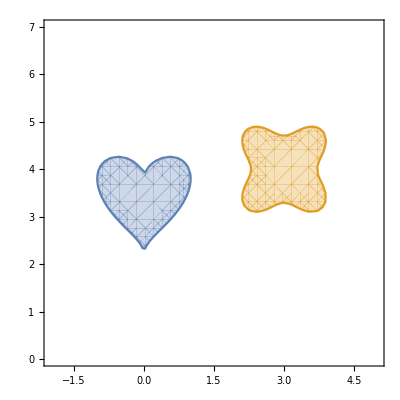

Pro najití nejkratší vzdálenosti potřebujeme minimalizovat odmocninu z f, potažmo tedy samotnou f:

```mathematica
f = (x1 - y1)^2 + (x2 - y2)^2;
```

```mathematica
l=Piecewise[{{-λ^2/(2ρ),λ+ρ*g<= ρ},{λ(g-1)+ρ/2(g-1)^2,λ+ρ*g> ρ}}];
```

```mathematica
L=f+ReplaceAll[ReplaceAll[l,g->g1],λ->λ1]+ReplaceAll[ReplaceAll[l,g->g2],λ->λ2];
```

```mathematica
Df=D[L,{{x1,x2,y1,y2,λ1,λ2}}];
```

```mathematica
D2f=D[L,{{x1,x2,y1,y2,λ1,λ2},2}];
```

```mathematica
ρ=0.1;
```

```mathematica
{x1,x2,y1,y2,λ1,λ2}={1.,4.,2.,3.,0.,0.};
```

## Výpočet

```mathematica
i=0; (* iterace pres i, ve funkci While muzeme snadno upravit presnost a pocet iteraci *)
history1={{x1,x2}};
history2={{y1,y2}};
While[Sqrt[Df.Df]>10^-10&&i≤15,
dx=-Inverse[D2f].Df;
{x1,x2,y1,y2,λ1,λ2}={x1,x2,y1,y2,λ1,λ2}+dx;
AppendTo[history1,{x1,x2}];
AppendTo[history2,{y1,y2}];
i=i+1;
Print["i=",i,"xy",{x1,x2,y1,y2,λ1,λ2}, "|Δxy|=",Sqrt[dx.dx],"|DfDxy|=",Sqrt[Df.Df]]

]
```

i=1xy{1.37206,2.85811,2.1019,3.10345,0.825503,1.52688}|Δxy|=2.11572|DfDxy|=164.593

i=2xy{1.16471,3.41979,2.15916,3.16638,0.792571,1.05414}|Δxy|=0.768302|DfDxy|=53.0465

i=3xy{1.00971,3.58089,2.17289,3.19633,0.978019,0.270486}|Δxy|=0.836399|DfDxy|=9.46047

i=4xy{0.967713,3.58198,2.14111,3.2384,1.06493,0.0444928}|Δxy|=0.251338|DfDxy|=1.90186

i=5xy{0.982254,3.63517,2.05523,3.39567,0.99322,0.0483698}|Δxy|=0.200774|DfDxy|=8.57382

i=6xy{0.983324,3.64735,2.0969,3.41045,1.03534,0.112674}|Δxy|=0.0895209|DfDxy|=2.44593

i=7xy{0.986419,3.66243,2.10456,3.44636,1.04537,0.0785522}|Δxy|=0.0533856|DfDxy|=0.423529

i=8xy{0.988815,3.67558,2.10949,3.47807,1.05303,0.0777255}|Δxy|=0.0355991|DfDxy|=0.126612

i=9xy{0.989073,3.67768,2.11147,3.4831,1.05567,0.0784694}|Δxy|=0.00642361|DfDxy|=0.00522129

i=10xy{0.989087,3.67778,2.11155,3.48333,1.05578,0.0784704}|Δxy|=0.000290237|DfDxy|=9.95144×10^-6

i=11xy{0.989087,3.67778,2.11155,3.48333,1.05579,0.0784704}|Δxy|=5.67386×10^-7|DfDxy|=3.94177×10^-11